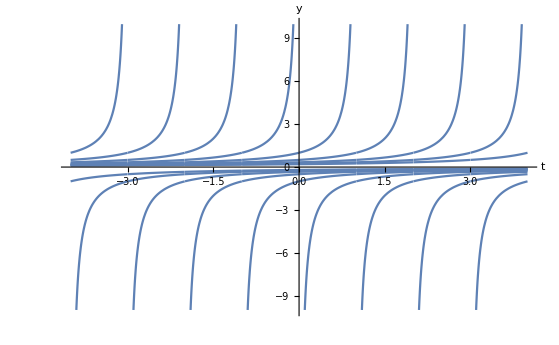
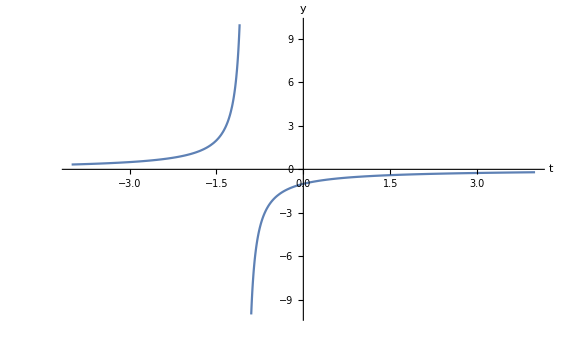
```mathematica
Equazione iniziale: y'=y^2

solution=DSolve[y'[t]==y[t]^2,y[t],t]
{{y[t]->1/(-t-C[1])}}
f[t_]=y[t]/.solution[[1]]
F[t_]=Table[f[t]/.C[1]->j, {j,-5,5}]
Plot[F[t],{t,-4,4},AxesLabel->{t,y},PlotRange->{-10,10}]
-Graphics-


Condizione data: y(0)=1

cauchy=DSolve[{y'[t]==y[t]^2,y[0]==-1},y[t],t]
{{y[t]->1/(-1-t)}}
g[t_]=y[t]/.cauchy[[1]]
Plot[g[t],{t,-4,4},AxesLabel->{t,y},PlotRange->{-10,10}]
-Graphics-
```